# Pseudo Mastery Name : Dhruvit Manojkumar Mavani

## Algorithm 20.1

```mathematica
luDecomposition[A_]:=Module[{m,U,L,ljk,j,k},
m=Length[A];
U=A;
L=IdentityMatrix[m];
For[k=1,k<=m-1,k++,For[j=k+1,j<=m,j++,ljk=U[[j,k]]/U[[k,k]];
L[[j,k]]=ljk;
U[[j,k;;m]]=U[[j,k;;m]]-ljk U[[k,k;;m]];];];
{L,U}];
```

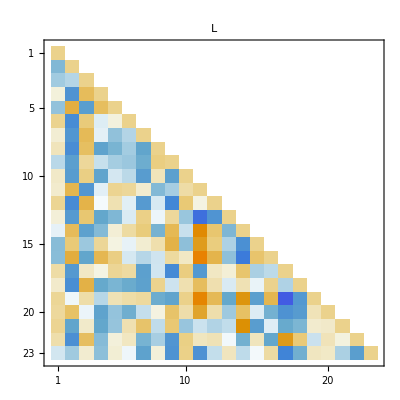

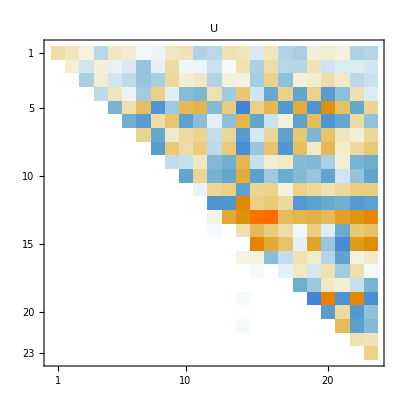

```mathematica
m=23;
A = RandomReal[{-1,1},{m,m}];
{L,U}=luDecomposition[A];
MatrixPlot[L,PlotLabel->"L"]
MatrixPlot[U,PlotLabel->"U"]
```

```mathematica
Norm[A-L.U]
```

8.18638×10^-14